```mathematica
SetDirectory[NotebookDirectory[]];
Guderley=Import["Snapshot.csv","CSV"];
```

```mathematica
u={};
For[i=0,i<Length[Guderley],i++;u=Append[u,{Guderley[[i]][[1]],Guderley[[i]][[2]]}]]
c={};
For[i=0,i<Length[Guderley],i++;c=Append[c,{Guderley[[i]][[1]],Guderley[[i]][[3]]}]]
ρ={};
For[i=0,i<Length[Guderley],i++;ρ=Append[ρ,{Guderley[[i]][[1]],Guderley[[i]][[4]]}]]
T={};
For[i=0,i<Length[Guderley],i++;T=Append[T,{Guderley[[i]][[1]],Guderley[[i]][[5]]}]]
P={};
For[i=0,i<Length[Guderley],i++;P=Append[P,{Guderley[[i]][[1]],Guderley[[i]][[6]]}]]
λii={};
For[i=0,i<Length[Guderley],i++;λii=Append[λii,{Guderley[[i]][[1]],Guderley[[i]][[7]]}]]
τii={};
For[i=0,i<Length[Guderley],i++;τii=Append[τii,{Guderley[[i]][[1]],Guderley[[i]][[8]]}]]
LogΛ={};
For[i=0,i<Length[Guderley],i++;LogΛ=Append[LogΛ,{Guderley[[i]][[1]],Guderley[[i]][[9]]}]]
λD={};
For[i=0,i<Length[Guderley],i++;λD=Append[λD,{Guderley[[i]][[1]],Guderley[[i]][[10]]}]]
```

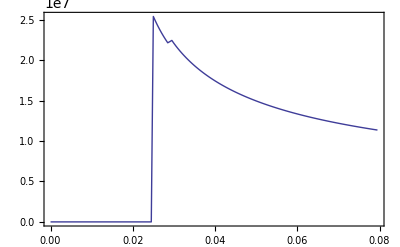

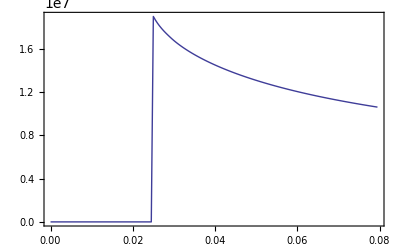

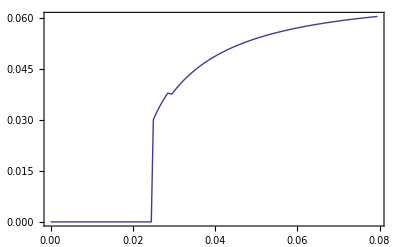

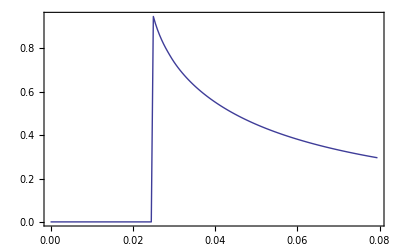

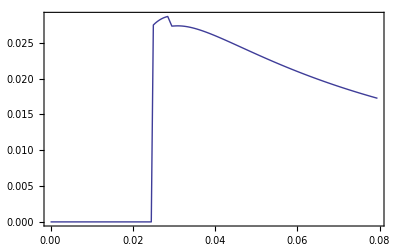

```mathematica
ListLinePlot[u,Frame->True,PlotRange->All]
ListLinePlot[c,Frame->True,PlotRange->All]
ListLinePlot[ρ,Frame->True,PlotRange->All]
ListLinePlot[T,Frame->True,PlotRange->All]
ListLinePlot[P,Frame->True,PlotRange->All]
```

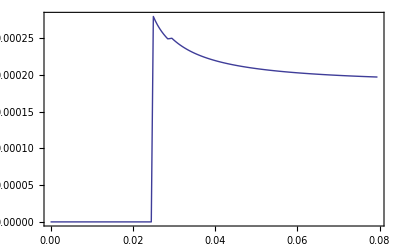

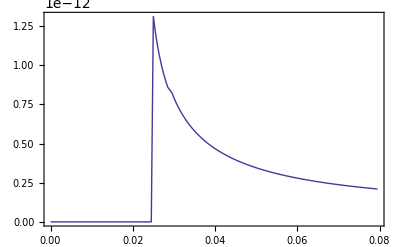

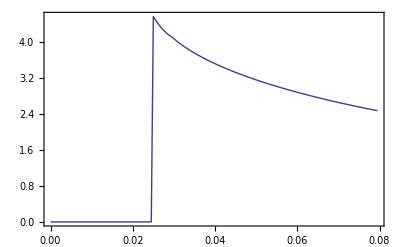

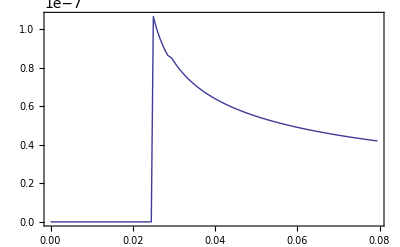

```mathematica
ListLinePlot[λii,Frame->True,PlotRange->All]
ListLinePlot[τii,Frame->True,PlotRange->All]
ListLinePlot[LogΛ,Frame->True,PlotRange->All]
ListLinePlot[λD,Frame->True,PlotRange->All]
```